```mathematica
(* find leap year *)

leapYear[x_]:=If[
Mod[x,4]≠0,Print[x," is not a Leap Year"],
If[Mod[x,100]≠0,Print[x," is a Leap Year"],
If[Mod[x,400]≠0,Print[x," is not a Leap Year"],
Print[x," is a Leap Year"]
]
]
]
```

```mathematica
leapYear[1987]
```

1987 is not a Leap Year

```mathematica
leapYear[6040]
```

6040 is a Leap Year

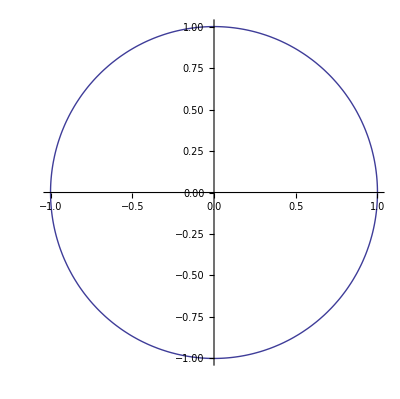
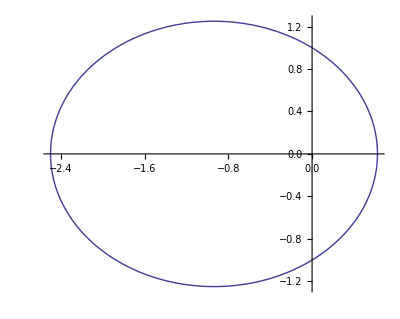
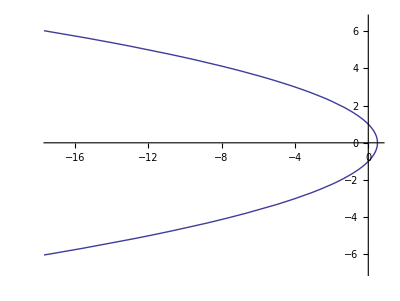
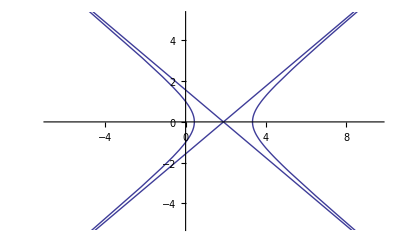

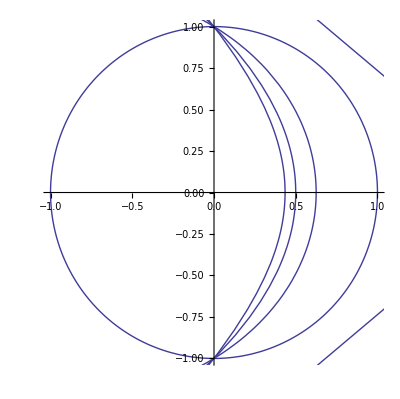

```mathematica
(* palanetary orbit *)

r[ϕ_]:=Subscript[r, 0]/(1+ϵ Cos[ϕ]);
x[ϕ_]:=r[ϕ] Cos[ϕ];
y[ϕ_]:=r[ϕ] Sin[ϕ];

ParametricPlot[{x[ϕ],y[ϕ]}/.{Subscript[r, 0]->1,ϵ->#},
{ϕ,0,2π},PlotTheme->"Classic"]&/@{0,0.6,1,1.3}

Show[
ParametricPlot[{x[ϕ],y[ϕ]}/.{Subscript[r, 0]->1,ϵ->#},
{ϕ,0,2π},PlotTheme->"Classic"]&/@{0,0.6,1,1.3}
]
```

```mathematica
z
```

z